```mathematica
data={{12.,1.},{74.,2.},{113.,3.}}
data2={{12.,1.},{74.,1.86},{113.,2.68}}
points=Point[data+{{1900,0},{1900,0},{1900,0}}]
points2=Point[data2+{{1900,0},{1900,0},{1900,0}}]
```

{{12.,1.},{74.,2.},{113.,3.}}

{{12.,1.},{74.,1.86},{113.,2.68}}

Point[{{1912.,1.},{1974.,2.},{2013.,3.}}]

Point[{{1912.,1.},{1974.,1.86},{2013.,2.68}}]

```mathematica
model=a/(1+ Exp[-b (t-t0)])
```

a/(1+ⅇ^(-b (t-t0)))

```mathematica
fit=FindFit[data,model,{{a,10},{b,.01},{t0,200}},t]
fit2=FindFit[data2,model,{{a,10},{b,.01},{t0,200}},t]
```

{a→16.0653,b→0.0122876,t0→232.743}

{a→14.7406,b→0.0110518,t0→249.098}

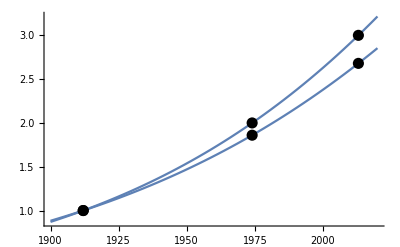

```mathematica
Show[grapha,graph2a,Graphics[{PointSize[0.02],points,points2}]]
```

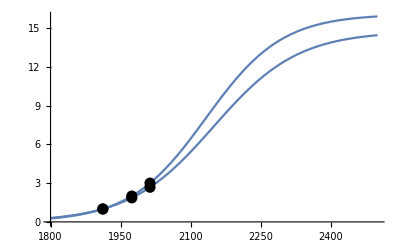

```mathematica
Show[graph,graph2,Graphics[{PointSize[0.02],points,points2}]]
```

```mathematica
Show[graph2,Graphics[{PointSize[0.02],Point[data2+{{1900,0},{1900,0},{1900,0}}]}]]
```

```mathematica
trend[x_]=model/.fit/.{t->(x-1900)};
```

```mathematica
trend2[x_]=model/.fit2/.{t->(x-1900)};
```

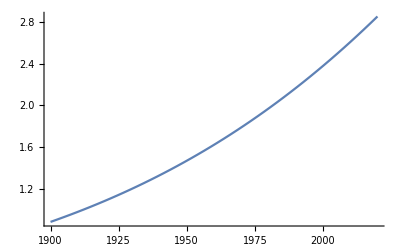

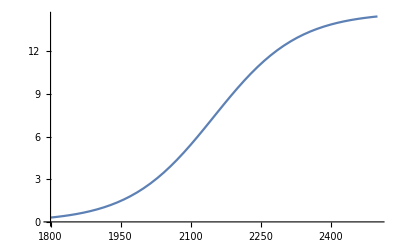

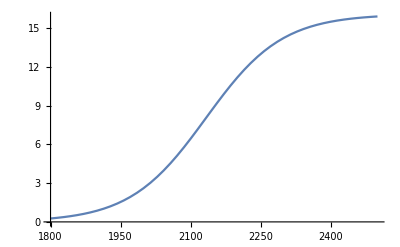

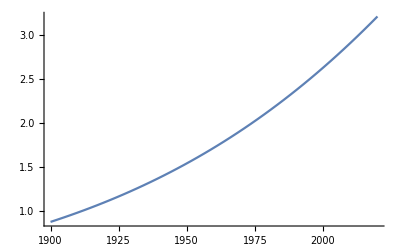

```mathematica
graph2a=Plot[trend2[t],{t,1900,2020}]
graph2=Plot[trend2[t],{t,1800,2500}]
graph=Plot[trend[t],{t,1800,2500}]
grapha=Plot[trend[t],{t,1900,2020}]
```